```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/yunqiguo/Document/CS249_2/project/249-Sun/src

```mathematica
purity[c_,w_]:=Module[{inter},
inter=Table[Length@Intersection[c[[i]],w[[j]]],{i,Length@c},{j,Length@w}];
Return@N[(Total@(Max/@inter))/(Total@(Length/@c))]
]
```

```mathematica
<<../data/edges.mx
```

```mathematica
<<../data/top5.mx
```

```mathematica
clustering=Import["test.txt","Data"];
```

```mathematica
clustering=ToExpression/@StringSplit[clustering," "];
```

```mathematica
g=Graph[edges];
```

```mathematica
distance=GraphDistanceMatrix[g];
```

```mathematica
vDic = Association@Table[#[[i]]->i,{i,Length@#}]&@VertexList[g];
```

```mathematica
am=Normal@AdjacencyMatrix[g];
```

```mathematica
communities=FindGraphPartition[g,1500];
```

```mathematica
(*communities=FindGraphCommunities[g,Method->"Modularity"];*)
```

```mathematica
(*communities=clustering;*)
```

```mathematica
Length@communities
```

1500

```mathematica
communityDistanceMatrix=Table[N@Mean@Flatten@distance[[vDic/@communities[[i]],vDic/@communities[[j]]]],{i,Length@communities},{j,Length@communities}];
```

```mathematica
g2=WeightedAdjacencyGraph[1/communityDistanceMatrix];
```

```mathematica
(*Export["communityDistanceMatrix.csv",communityDistanceMatrix//TableForm];*)
```

```mathematica
communities4=FindGraphCommunities[g2,Method->"Spectral"];
```

```mathematica
Length@communities4
```

21

```mathematica
c4Size=Length@communities4;
```

```mathematica
distance2=GraphDistanceMatrix[g2];
```

```mathematica
vDic2= Association@Table[#[[i]]->i,{i,Length@#}]&@VertexList[g2];
```

```mathematica
communityDistanceMatrix2=Table[N@Mean@Flatten@distance2[[vDic2/@communities4[[i]],vDic2/@communities4[[j]]]],{i,c4Size},{j,c4Size}];
```

```mathematica
nearests=Position[#,Min[#]][[1,1]]&/@ communityDistanceMatrix2[[6;;,1;;5]];
```

```mathematica
communities5=Table[
Join[communities4[[i]],Flatten@ communities4[[ Position[nearests,i][[All,1]] +5]]],{i,5}];
```

```mathematica
purity[Flatten[communities[[#]]]&/@communities5,top5]
```

0.639856

```mathematica
result={};
For[bd=4,bd<8,bd+=0.1,
bound=bd;
filter[t_]:=If[t<bound,1,0];
adjancyMaptrix=Map[filter,communityDistanceMatrix,{2}];
g3=AdjacencyGraph[adjancyMaptrix];
communities2=FindGraphPartition[g3,5];
communities3=Flatten[communities[[#]]]&/@communities2;
AppendTo[result,{bd,purity[communities3,top5]}];
]
```

```mathematica
Dynamic[bd]
```

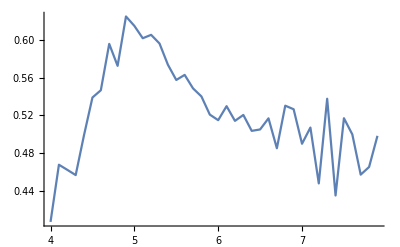

```mathematica
ListPlot[result,Joined->True]
```

Baseline

```mathematica
communities0=FindGraphPartition[g,5];
```

```mathematica
(*communities0=FindGraphCommunities[g];*)
```

```mathematica
purity[communities0,top5]
```

0.567999

use spectral method

```mathematica
g[
```

```mathematica
(*adjancy=1/communityDistanceMatrix;
Table[adjancy[[i,i]]=0,{i,Length@adjancy}];
k=DiagonalMatrix@(Total/@adjancy);
m=Total@Flatten[k];*)
```

```mathematica
communities2=FindGraphCommunities[g,Method->"Spectral"];
```

```mathematica
communities6 =Flatten@ToExpression@ Import["communities2.txt","Data"];
```

```mathematica
communities7 =Flatten[ Position[communities6,#]&/@Range[5],{3}][[1]];
```

```mathematica
communities3=Flatten[communities[[#]]]&/@communities7;
```

```mathematica
Length/@communities3
```

{4253,4159,6953,2195,6933}

```mathematica
purity[communities3,top5]
```

0.406728

Baseline

```mathematica
communities=FindGraphCommunities[g,Method->"Modularity"];
```

```mathematica
communityDistanceMatrix=Table[N@Mean@Flatten@distance[[vDic/@communities[[i]],vDic/@communities[[j]]]],{i,Length@communities},{j,Length@communities}];
```

```mathematica
nearests=Position[#,Min[#]][[1,1]]&/@ communityDistanceMatrix[[6;;,1;;5]];
```

```mathematica
communitiesFinal=Table[
Join[communities[[i]],Flatten@ communities[[ Position[nearests,i][[All,1]] +5]]],{i,5}];
```

```mathematica
purity[communitiesFinal,top5]
```

0.500674